```mathematica
GenerateAllGraphsOfSize2[k_]:=Block[{edges=Subsets[Range[k],{2}],combinations, total, current,result},
Print["Number of edges " <>ToString[Length[edges]]];
combinations=Subsets[edges,3*k-6];
total=Length[combinations];
Print["Number of combinations " <>ToString[total]];
current=0;
Monitor[
result=Select[
Table[
current++;
Graph[Range[k],e, VertexLabels->"Name"],
{e,combinations}
],
ConnectedGraphQ[#]&
],
{current,total}
];
PrintTemporary["Graphs found ", k, " --", Length[result]];
result
]
```

```mathematica
all8=GenerateAllGraphsOfSize2[8];Length[all8]
```

Number of edges 21

Number of combinations 2069256

$Aborted

```mathematica
min8=all8;
```

```mathematica
Length[min8]
```

1866256

```mathematica
min8b=Parallelize[Select[min8,PlanarGraphQ[#]&]];Length[min8b]
```

1597690

```mathematica
min8c=Parallelize[Select[min8b,MaximalPlanarQ[#]&]];Length[min8c]
```

5712

```mathematica
min8d=Parallelize[Select[min8c,ChromaticPolynomial[#,4]==24&]];Length[min8d]
```

4620

```mathematica
min8Uniq=Tally[min8d,IsomorphicGraphQ]
```

## This is for 7 nodes

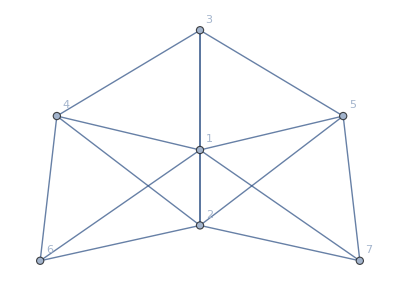
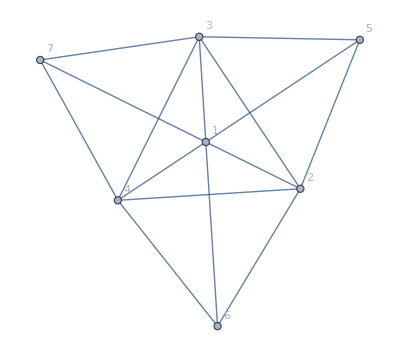
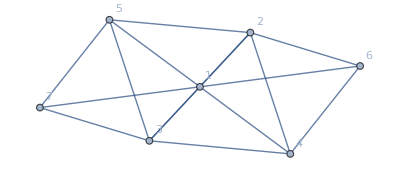
{{-Graphics-,1260},{-Graphics-,840},{-Graphics-,2520}}

```mathematica
min8Uniq=Tally[min8d,IsomorphicGraphQ]
```

```mathematica
TableForm[Map[Map[Last,#]&,Map[FormulaLevels[FindFullFormula[#]]&,Map[First,min8Uniq]]],TableDepth->2]
```

1 | 7 | 6 | 1
1 | 7 | 6 | 1
1 | 7 | 6 | 1

```mathematica
TableForm[Map[GatherBy[FindFullFormula[#],SymbolLevel[#]&]&,Map[First,min8Uniq]],TableDepth->3]
```

{v1x2x3x4x5x6x7} | {v1x2x3x4x5x67}
{v1x2x3x4x56x7}
{v1x2x3x47x5x6}
{v1x2x3x45x6x7}
{v1x2x37x4x5x6}
{v1x2x36x4x5x7} | {v1x2x3x47x56}
{v1x2x3x45x67}
{v1x2x37x4x56}
{v1x2x37x45x6}
{v1x2x367x4x5}
{v1x2x36x47x5}
{v1x2x36x45x7} | {v1x2x367x45}
{v1x2x3x4x5x6x7} | {v1x2x3x4x5x67}
{v1x2x3x4x57x6}
{v1x2x3x4x56x7}
{v1x2x3x45x6x7}
{v1x2x36x4x5x7}
{v1x27x3x4x5x6} | {v1x2x3x4x567}
{v1x2x3x45x67}
{v1x2x36x4x57}
{v1x2x36x45x7}
{v1x27x3x4x56}
{v1x27x3x45x6}
{v1x27x36x4x5} | {v1x27x36x45}
{v1x2x3x4x5x6x7} | {v1x2x3x4x5x67}
{v1x2x3x4x56x7}
{v1x2x3x47x5x6}
{v1x2x3x45x6x7}
{v1x2x36x4x5x7}
{v1x27x3x4x5x6} | {v1x2x3x47x56}
{v1x2x3x45x67}
{v1x2x36x47x5}
{v1x2x36x45x7}
{v1x27x3x4x56}
{v1x27x3x45x6}
{v1x27x36x4x5} | {v1x27x36x45}

```mathematica
Subsets[Subsets[Range[8],{2}],{3*8-6}]//Length
```

13123110